```mathematica
DSolve[p^2/(2μ)ϕ[p]+I ℏ λ D[ϕ[p],p]-p^4/(32 μ^3)ϕ[p]==e ϕ[p],ϕ,p]
```

{{ϕ→Function[{p},ⅇ^(-(ⅈ (p^5/5-(16 p^3 μ^2)/3+32 e p μ^3))/(32 λ μ^3 ℏ)) C[1]]}}

```mathematica
ⅇ^((ⅈ ((16 p^3)/3+p^5/5-32 e p μ))/(32 λ μ ℏ))
```

```mathematica
{{ϕ->Function[{p},ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ)) C[1]]}}⟦1,1,2⟧
```

Function[{p},ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ)) C[1]]

```mathematica
m=5/2;
λ=π/2;
```

```mathematica
%2
```

Function[{p},ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ)) C[1]]

```mathematica
ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->m,ℏ->1}
```

ⅇ^((2 ⅈ (-5 e p+p^3/3))/(5 π))

```mathematica
FullSimplify[ⅇ^((2 ⅈ (-5 e p+p^3/3))/(5 π))]
```

ⅇ^((2 ⅈ p (-15 e+p^2))/(15 π))

```mathematica
D[ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ)),p]
```

```mathematica
Solve[(ⅈ ⅇ^((ⅈ (p^3/3-2 e p μ))/(π μ ℏ)) (p^2-2 e μ))/(π μ ℏ)==0/.p->0,e]
```

{{e→0}}

```mathematica
Solve[ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))==0/.p->0,e]
```

{}

```mathematica
norm=Simplify@Integrate[1,{p,-∞,∞},Assumptions->e/(λ ℏ)∈Reals&&1/(λ μ ℏ)∈Reals]
```

∞

```mathematica
-Integrate[p^4/(32 μ^3 norm)(*/.{μ->5/2,λ->π/2,ℏ->1,e->0.805086}*),{p,-∞,∞}]
```

0

```mathematica
ExpToTrig[ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))]
```

Cos[(e p)/(λ ℏ)-p^3/(6 λ μ ℏ)]-ⅈ Sin[(e p)/(λ ℏ)-p^3/(6 λ μ ℏ)]

```mathematica
ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1,e->0.8}
```

ⅇ^((2 ⅈ (-4. p+p^3/3))/(5 π))

```mathematica
ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1,e->0.89,p->100}
```

-0.137847-0.990453 ⅈ

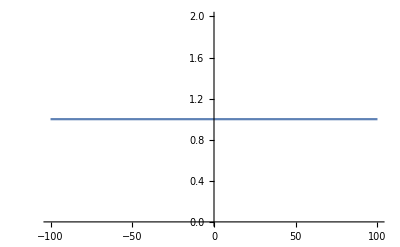

```mathematica
Plot[Abs[ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))]/.{μ->5/2,λ->π/2,ℏ->1,e->0.89},{p,-100,100}]
```

```mathematica
Integrate[E^(I p x)ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1},{p,-∞,∞}]
```

ConditionalExpression[2^(2/3) 5^(1/3) π^(4/3) AiryAi[((5/2)^(1/3) (-2 e+π x))/π^(2/3)],2 Im[e]==π Im[x]]

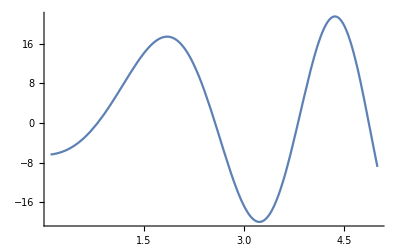

```mathematica
Plot[Evaluate[D[2^(2/3) 5^(1/3) π^(4/3) AiryAi[((5/2)^(1/3) (-2 e+π x))/π^(2/3)],x]]/.x->0,{e,0.1,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

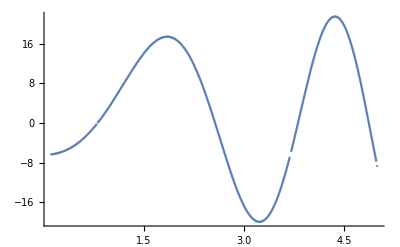

```mathematica
Block[{range=1000},Plot[NIntegrate[I p E^(I p x)ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1}/.x->0,{p,-range,range},MaxRecursion->50],{e,0.1,5}]]
```

```mathematica
Integrate[E^(I p x)ⅇ^((ⅈ (p^5/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1},{p,-∞,∞}]
```

ConditionalExpression[2 Gamma[6/5] (1/4 √(5/8+(√5)/8) (-1+√5) (1+√5) ((15 π)/2)^(1/5) HypergeometricPFQ[{},{1/5,3/10,2/5,1/2,7/10,4/5,9/10},(9 (-2 e+π x)^10)/(400000000 π^8)]-(3^(1/5) (-1+√5) (1+√5) √(5+√5) (-2 e+π x)^5 HypergeometricPFQ[{},{7/10,4/5,9/10,6/5,13/10,7/5,3/2},(9 (-2 e+π x)^10)/(400000000 π^8)])/(128 2^(7/10) 5^(4/5) π^(19/5)))+2 Gamma[2/5] (-(3^(2/5) √(5-√5) (-1+√5) (1+√5) (-2 e+π x) HypergeometricPFQ[{},{3/10,2/5,1/2,3/5,4/5,9/10,11/10},(9 (-2 e+π x)^10)/(400000000 π^8)])/(8 2^(9/10) (5 π)^(3/5))+(√(5-√5) (-1+√5) (1+√5) (-2 e+π x)^6 HypergeometricPFQ[{},{4/5,9/10,11/10,13/10,7/5,3/2,8/5},(9 (-2 e+π x)^10)/(400000000 π^8)])/(640 2^(9/10) 15^(3/5) π^(23/5)))+2 Gamma[3/5] (((5/2)^(1/10) 3^(3/5) √(5-√5) (-1+√5) (-2 e+π x)^2 HypergeometricPFQ[{},{2/5,1/2,3/5,7/10,9/10,11/10,6/5},(9 (-2 e+π x)^10)/(400000000 π^8)])/(8 (-5+√5) π^(7/5))+(3^(3/5) √(5-√5) (-1+√5) (1+√5) (-2 e+π x)^7 HypergeometricPFQ[{},{9/10,11/10,6/5,7/5,3/2,8/5,17/10},(9 (-2 e+π x)^10)/(400000000 π^8)])/(17920 2^(1/10) 5^(2/5) π^(27/5)))+2 Gamma[4/5] (((-1+√5) (1+√5) √(5+√5) (-2 e+π x)^3 HypergeometricPFQ[{},{1/2,3/5,7/10,4/5,11/10,6/5,13/10},(9 (-2 e+π x)^10)/(400000000 π^8)])/(32 2^(3/10) 15^(1/5) π^(11/5))-((-1+√5) (1+√5) √(5+√5) (-2 e+π x)^8 HypergeometricPFQ[{},{11/10,6/5,13/10,3/2,8/5,17/10,9/5},(9 (-2 e+π x)^10)/(400000000 π^8)])/(35840 2^(3/10) 15^(1/5) π^(31/5))),2 Im[e]==π Im[x]]

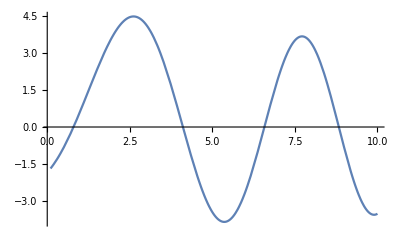

```mathematica
Plot[2 Gamma[6/5] (-(15^(1/5) (-1+√5) (1+√5) √(5+√5) e^4 HypergeometricPFQ[{},{7/10,4/5,9/10,6/5,13/10,7/5,3/2},(9 e^10)/(390625 π^8)])/(8 2^(7/10) π^(14/5))-(√(5/8+(√5)/8) (-1+√5) (1+√5) e^9 HypergeometricPFQ[{},{6/5,13/10,7/5,3/2,17/10,9/5,19/10},(9 e^10)/(390625 π^8)])/(14 2^(1/5) 15^(4/5) π^(34/5))-((-1+√5) (1+√5) √(5+√5) e^14 HypergeometricPFQ[{},{17/10,9/5,19/10,11/5,23/10,12/5,5/2},(9 e^10)/(390625 π^8)])/(19110 2^(7/10) 15^(4/5) π^(54/5)))+2 Gamma[2/5] (-(√(5-√5) (-1+√5) (1+√5) (3 π)^(2/5) HypergeometricPFQ[{},{3/10,2/5,1/2,3/5,4/5,9/10,11/10},(9 e^10)/(390625 π^8)])/(8 2^(9/10) 5^(3/5))-(3^(2/5) √(5-√5) (-1+√5) (1+√5) e^5 HypergeometricPFQ[{},{4/5,9/10,11/10,13/10,7/5,3/2,8/5},(9 e^10)/(390625 π^8)])/(10 2^(9/10) 5^(3/5) π^(18/5))-(√(5-√5) (-1+√5) (1+√5) e^10 HypergeometricPFQ[{},{13/10,7/5,3/2,8/5,9/5,19/10,21/10},(9 e^10)/(390625 π^8)])/(330 2^(9/10) 15^(3/5) π^(38/5))-(√(5-√5) (-1+√5) (1+√5) e^15 HypergeometricPFQ[{},{9/5,19/10,21/10,23/10,12/5,5/2,13/5},(9 e^10)/(390625 π^8)])/(300300 2^(9/10) 15^(3/5) π^(58/5)))+2 Gamma[3/5] (-((5/2)^(1/10) 3^(3/5) √(5-√5) (-1+√5) e HypergeometricPFQ[{},{2/5,1/2,3/5,7/10,9/10,11/10,6/5},(9 e^10)/(390625 π^8)])/(2 (-5+√5) π^(2/5))+(3^(3/5) √(5-√5) (-1+√5) (1+√5) e^6 HypergeometricPFQ[{},{9/10,11/10,6/5,7/5,3/2,8/5,17/10},(9 e^10)/(390625 π^8)])/(40 2^(1/10) 5^(2/5) π^(22/5))-((2/5)^(9/10) √(5-√5) (-1+√5) e^11 HypergeometricPFQ[{},{7/5,3/2,8/5,17/10,19/10,21/10,11/5},(9 e^10)/(390625 π^8)])/(231 3^(2/5) (-5+√5) π^(42/5))+(√(5-√5) (-1+√5) (1+√5) e^16 HypergeometricPFQ[{},{19/10,21/10,11/5,12/5,5/2,13/5,27/10},(9 e^10)/(390625 π^8)])/(2748900 2^(1/10) 15^(2/5) π^(62/5)))+2 Gamma[4/5] ((3^(4/5) (-1+√5) (1+√5) √(5+√5) e^2 HypergeometricPFQ[{},{1/2,3/5,7/10,4/5,11/10,6/5,13/10},(9 e^10)/(390625 π^8)])/(8 2^(3/10) 5^(1/5) π^(6/5))+((-1+√5) (1+√5) √(5+√5) e^7 HypergeometricPFQ[{},{11/10,6/5,13/10,3/2,8/5,17/10,9/5},(9 e^10)/(390625 π^8)])/(35 2^(3/10) 15^(1/5) π^(26/5))+((-1+√5) (1+√5) √(5+√5) e^12 HypergeometricPFQ[{},{3/2,8/5,17/10,9/5,21/10,11/5,23/10},(9 e^10)/(390625 π^8)])/(10010 2^(3/10) 15^(1/5) π^(46/5))+((-1+√5) (1+√5) √(5+√5) e^17 HypergeometricPFQ[{},{21/10,11/5,23/10,5/2,13/5,27/10,14/5},(9 e^10)/(390625 π^8)])/(15315300 2^(3/10) 15^(1/5) π^(66/5))),{e,0.1,10}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

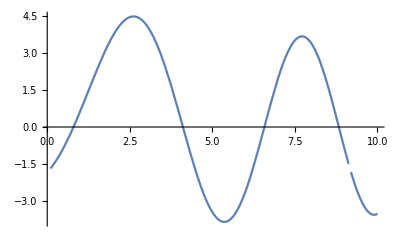

```mathematica
Block[{range=1000},Plot[NIntegrate[I p E^(I p x)ⅇ^((ⅈ (p^5/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1}/.x->0,{p,-range,range},MaxRecursion->50],{e,0.1,10}]]
```

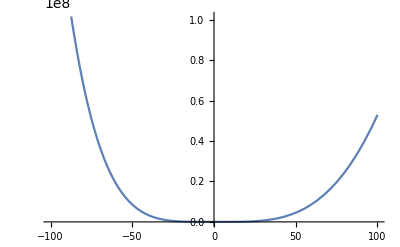

```mathematica
Plot[Abs[p^4 E^(I p x)ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1,x->1,e->0.8-0.01I}],{p,-100,100}]
```

```mathematica
Integrate[p^4 E^(I p x)ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1},{p,0,∞}]
```

ConditionalExpression[1/12773376 25 (1241856 ⅈ (3 ⅈ+√3) π^2 ((-2 e+π x)^(3/2))^(2/3) BesselI[-2/3,(√10 (-2 e+π x)^(3/2))/(3 π)]+(88704 ⅈ √10 (3 ⅈ+√3) π (-2 e+π x)^3 BesselI[1/3,(√10 (-2 e+π x)^(3/2))/(3 π)])/(((-2 e+π x)^(3/2))^(1/3))+(1951488 (3+ⅈ √3) π^2 (-2 e+π x)^2 BesselI[2/3,(√10 (-2 e+π x)^(3/2))/(3 π)])/(((-2 e+π x)^(3/2))^(2/3))+(88704 ⅈ √10 (-3 ⅈ+√3) π (-2 e+π x)^(7/2) BesselI[5/3,(√10 (-2 e+π x)^(3/2))/(3 π)])/(((-2 e+π x)^(3/2))^(2/3))+532224 (3-ⅈ √3) π^2 ((-2 e+π x)^(3/2))^(2/3) BesselJ[-2/3,(√10 (-2 e+π x)^(3/2))/(3 π)]+(88704 ⅈ √10 (3 ⅈ+√3) π (2 e-π x)^3 BesselJ[1/3,(√10 (-2 e+π x)^(3/2))/(3 π)])/(((-2 e+π x)^(3/2))^(1/3))-(532224 ⅈ (-3 ⅈ+√3) π^2 (-2 e+π x)^2 BesselJ[2/3,(√10 (-2 e+π x)^(3/2))/(3 π)])/(((-2 e+π x)^(3/2))^(2/3))-(88704 √10 (3+ⅈ √3) π (-2 e+π x)^(7/2) BesselJ[5/3,(√10 (-2 e+π x)^(3/2))/(3 π)])/(((-2 e+π x)^(3/2))^(2/3))-(5940 2^(1/3) 3^(1/6) 5^(2/3) (-2 e+π x)^9 Gamma[8/3] HypergeometricPFQ[{},{5/3,13/6,5/2},(25 (-2 e+π x)^6)/(5184 π^4)])/π^(13/3)+(1980 ⅈ 2^(1/3) 15^(2/3) (-2 e+π x)^9 Gamma[8/3] HypergeometricPFQ[{},{5/3,13/6,5/2},(25 (-2 e+π x)^6)/(5184 π^4)])/π^(13/3)+(175 2^(2/3) 3^(5/6) 5^(1/3) (-2 e+π x)^11 Gamma[1/3] HypergeometricPFQ[{},{7/3,5/2,17/6},(25 (-2 e+π x)^6)/(5184 π^4)])/π^(17/3)+(175 ⅈ 2^(2/3) 15^(1/3) (-2 e+π x)^11 Gamma[1/3] HypergeometricPFQ[{},{7/3,5/2,17/6},(25 (-2 e+π x)^6)/(5184 π^4)])/π^(17/3)-(5987520 ⅈ (-2 e+π x)^4 HypergeometricPFQ[{2},{5/6,7/6,4/3,5/3},(25 (-2 e+π x)^6)/(5184 π^4)])/π-9580032 ⅈ π (-2 e+π x) HypergeometricPFQ[{1,3/2},{1/3,1/2,2/3,5/6,7/6},(25 (-2 e+π x)^6)/(5184 π^4)]),π Im[x]>2 Im[e]]

```mathematica
Evaluate[D[2^(2/3) 5^(1/3) π^(4/3) AiryAi[((5/2)^(1/3) (-2 e+π x))/π^(2/3)],x]]/.{e->2.56684,x->10000}
```

-1.63718189977957×10^-811205

```mathematica
Integrate[E^(I p x)ⅇ^((ⅈ (p^3/3-2 e p μ))/(2 λ μ ℏ)),{p,-∞,∞}]
```

ConditionalExpression[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3]),-π x+(2 e)/ℏ∈Reals&&1/(μ ℏ)∈Reals&&π Im[x]≥2 Im[e/ℏ]]

```mathematica
FullSimplify[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3])/.{μ->5/2,λ->π/2,ℏ->1}]
```

2^(2/3) 5^(1/3) π^(4/3) AiryAi[((5/2)^(1/3) (-2 e+π x))/π^(2/3)]

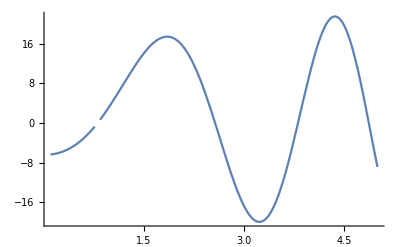

```mathematica
Plot[D[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+
9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3]),x]/.{x->0,μ->2.5,ℏ->1},{e,0.1,5}]
```

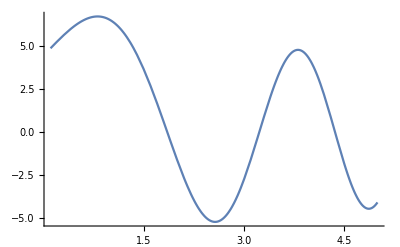

```mathematica
Plot[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3])/.{x->0,μ->2.5,ℏ->1},{e,0.1,5}]
```

```mathematica
FindRoot[D[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+
9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3]),x]==0/.{x->0,μ->2.5,ℏ->1},{e,2.5}]
```

{e→2.56684+1.65138×10^-16 ⅈ}

```mathematica
N[FullSimplify[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3])/.{μ->5/2,ℏ->1}]/.{x->10000000,e->2.56684}]
```

3.62383551613648415234872828251907425158`15.954589770191005*^-25658891275

```mathematica
N[1/(72 π^(7/3))μ (1/(μ^2 ℏ^2))^(1/6) ((48 π^(10/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 BesselI[-1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(5/3))+(48 π^(10/3) (2 e-π x ℏ) BesselI[1/3,(2 √μ (-2 e+π x ℏ)^(3/2))/(3 π ℏ)])/(((√μ (-2 e+π x ℏ)^(3/2))/ℏ)^(1/3))-4 3^(5/6) π^(5/3) x μ^2 (1/(μ^2 ℏ^2))^(2/3) ℏ (-2 e+π x ℏ)^2 Gamma[1/3]+4 3^(5/6) π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^3 Gamma[1/3]+(72 3^(1/6) e^2 π x μ (-2 e+π x ℏ) Gamma[2/3])/ℏ-(6 3^(1/6) μ (-2 e+π x ℏ)^4 Gamma[2/3])/ℏ^2+24 3^(5/6) e π^(2/3) μ^2 (1/(μ^2 ℏ^2))^(2/3) (-2 e+π x ℏ)^2 Gamma[4/3]+(72 3^(1/6) e^3 μ (2 e-π x ℏ) Gamma[5/3])/ℏ^2-54 3^(1/6) e π^2 x^2 μ (-2 e+π x ℏ) Gamma[5/3]+9 3^(1/6) π^3 x^3 μ ℏ (-2 e+π x ℏ) Gamma[5/3])/.{x->10000000000,μ->5/2,ℏ->1,e->2.56684}]
```

-1.231624914185740570707582048250186256100261402146393`15.954589770191005*^811405585267034

```mathematica
Integrate[E^(I(a p+b p^2+c p^5)),{p,-∞,∞}]
```

∫_(-∞)^∞ ⅇ^(ⅈ (a p+b p^2+c p^5))ⅆp

```mathematica
Expand[(p-x)^5][[3]]
```

p^5-5 p^4 x+10 p^3 x^2-10 p^2 x^3+5 p x^4-x^5

```mathematica
Solve[(Expand[(p-x)^5][[3]])/5==(16 (p-x)^3)/3,x]
```

{{x→1/8 (8 p-p^3)-(576 p^4-36 p^6)/(288 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))+1/8 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3)},{x→1/8 (8 p-p^3)+((1+ⅈ √3) (576 p^4-36 p^6))/(576 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))-1/16 (1-ⅈ √3) (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3)},{x→1/8 (8 p-p^3)+((1-ⅈ √3) (576 p^4-36 p^6))/(576 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))-1/16 (1+ⅈ √3) (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3)}}

```mathematica
(ⅈ (-80 e p+(16 p^3)/3+p^5/5))/(40 π)+ⅈ p x/.p->(p-s)/.{s->1/8 (8 p-p^3)-(576 p^4-36 p^6)/(288 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))+1/8 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3)}
```

1/(40 π)ⅈ (-80 e (p+1/8 (-8 p+p^3)+(576 p^4-36 p^6)/(288 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))-1/8 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))+16/3 (p+1/8 (-8 p+p^3)+(576 p^4-36 p^6)/(288 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))-1/8 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))^3+1/5 (p+1/8 (-8 p+p^3)+(576 p^4-36 p^6)/(288 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))-1/8 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))^5)+ⅈ (p+1/8 (-8 p+p^3)+(576 p^4-36 p^6)/(288 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3))-1/8 (-96 p^5+24 p^7-p^9+16 √2 √(18 p^10-p^12))^(1/3)) x

```mathematica
FullSimplify@%
```

1/40 ⅈ (1/π(-10 e (8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))+1/96 (8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))^3+1/163840(8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))^5)+5 (8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3)) x)

```mathematica
Integrate[E^(1/40 ⅈ (1/π(-10 e (8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))+1/96 (8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))^3+1/163840(8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))^5)+5 (8 p+p (-8+p^2)-(p^4 (-16+p^2))/((-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3))-(-96 p^5+24 p^7-p^9+16 √2 √(-p^10 (-18+p^2)))^(1/3)) x)),{p,-∞,∞}]
```

$Aborted

```mathematica
Integrate[E^(I p x)ⅇ^((ⅈ ((16 p^3)/3+p^5/5-32 e p μ))/(32 λ μ ℏ))/.{μ->5/2,λ->π/2,ℏ->1},{p,-∞,∞},PrincipalValue->True]
```

Integrate[ⅇ^((ⅈ (-80 e p+(16 p^3)/3+p^5/5))/(40 π)+ⅈ p x),{p,-∞,∞},PrincipalValue→True]

```mathematica
FullSimplify@(E^(I p x))ⅇ^(-(ⅈ (p^5/5-(16 p^3 μ^2)/3+32 e p μ^3))/(32 λ μ^3 ℏ))/.{μ->5/2,ℏ->1,λ->π/2}
```

ⅇ^(-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(250 π)+ⅈ p x)

```mathematica
range=100;
```

```mathematica
Int[e_?NumberQ,x_?NumberQ]:=NIntegrate[ⅇ^(-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(250 π)+ⅈ p x),{p,-range,range},MaxRecursion->20]
```

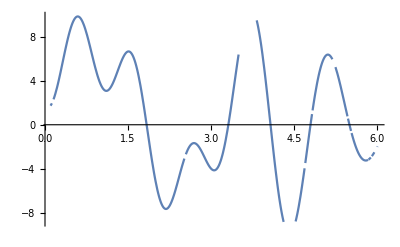

```mathematica
Plot[Int[e,0],{e,0.1,6},ImageSize->Full]
```

```mathematica
DInt[e_?NumberQ,x_?NumberQ]:=NIntegrate[ⅈ ⅇ^(-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(250 π)+ⅈ p x) p,{p,-range,range},MaxRecursion->20]
```

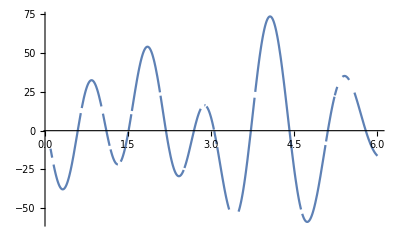

```mathematica
Plot[DInt[e,0],{e,0.1,6},ImageSize->Full]
```

```mathematica
Int[e_?NumberQ,x_?NumberQ]:=NIntegrate[ⅇ^(-(ⅈ (500000 e p-(10000 p^3)/3+p^5/5))/(250000 π)+ⅈ p x),{p,-range,range},MaxRecursion->20,WorkingPrecision->30,PrecisionGoal->15]
```

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (50029.6 p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

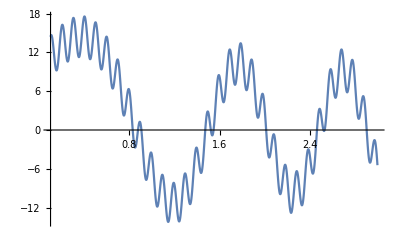

```mathematica
Plot[Block[{range=100000},Int[e,0]],{e,0.1,3},ImageSize->Full]
```

NIntegrate::precw: The precision of the argument function (ⅇ^(-(ⅈ (50029.6 p-(10000 p^3)/3+p^5/5))/(250000 π))) is less than WorkingPrecision (30.).

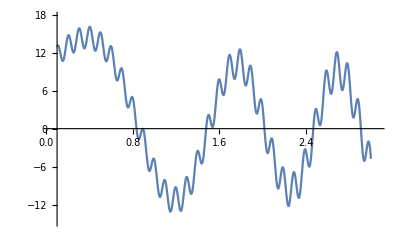

```mathematica
Plot[Int[e,0],{e,0.1,3},ImageSize->Full]
```

```mathematica
D[ⅇ^(-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(250 π)+ⅈ p x),x]
```

ⅈ ⅇ^(-(ⅈ (500 e p-(100 p^3)/3+p^5/5))/(250 π)+ⅈ p x) p

```mathematica
DInt[e_?NumberQ,x_?NumberQ]:=NIntegrate[ⅈ ⅇ^(-(ⅈ (500000 e p-(10000 p^3)/3+p^5/5))/(250000 π)+ⅈ p x) p,{p,-range,range},MaxRecursion->50]
```

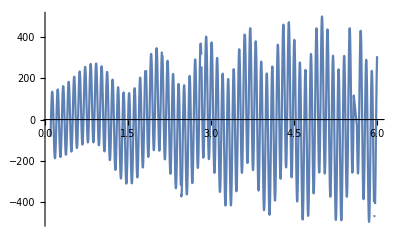

```mathematica
Plot[DInt[e,0],{e,0.1,6},ImageSize->Full]
```

```mathematica
FindRoot[Int[e,0]==0,{e,2}]
```

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 3.42568×10^-10+5.31769×10^-13 ⅈ 和 3.91614×10^-14.

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 2.31586×10^-16+3.49547×10^-16 ⅈ 和 3.92573×10^-14.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{e→2.01668-5.39277×10^-17 ⅈ}

```mathematica
FindRoot[DInt[e,0]==0,{e,2,3}]
```

NIntegrate::slwcon: 数值积分收敛速度太慢；可能是如下原因：奇点，积分值是 0，高度振荡的被积函数，或者 WorkingPrecision 太小.

General::stop: 在本次计算中，NIntegrate::slwcon 的进一步输出将被抑制.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 5.74916×10^-12-1.23512×10^-15 ⅈ 和 3.69319×10^-13.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 4.43839×10^-12-8.80849×10^-15 ⅈ 和 3.89009×10^-13.

NIntegrate::eincr: 策略 GlobalAdaptive 的全局误差已经增加了超过 400 次. 在数次计算被积函数后，全局误差应该单调递减. 可能是如下原因之一：工作精度对于指定的精度目标是不足的；被积函数高度振荡或者它不是一个（分段）平滑函数；或者积分的真实值为 0. 增加 GlobalAdaptive 选项 MaxErrorIncreases 的值可能产生一个发散的数值积分. 对于积分和误差估计，NIntegrate 得到 4.41383×10^-14+9.28424×10^-15 ⅈ 和 4.35812×10^-13.

General::stop: 在本次计算中，NIntegrate::eincr 的进一步输出将被抑制.

{e→2.84012-6.83341×10^-17 ⅈ}

```mathematica
eng={0.805086461614489,1.8476556810905445,2.5668413222583606,3.2304431281168653,3.809013929789016,4.3625428374845665,4.870464808536126,5.363098255348519,5.825756826509004,6.277737076397194,6.70790430744351,7.130019806467897,7.535251195372766,7.934103083695823,8.31933191642819,8.699327691820923,9.067998145417569,9.432264300165105,9.786900548704143,10.137755972462365,10.4802774360131,10.819501929975981,11.151411104213096,11.480408296873623,11.802909171492033,12.122810719862517,12.436886887723318,12.748622018806657,13.055090139396938,13.359433714546334,13.65898125610012,13.956587981343624,14.249800571429883,14.541229963384225,14.828611659801858,15.114346661981479,15.3963352727963,15.676796400134869,15.953775261960438,16.22933152641278,16.501638697825598,16.772616171813652,17.040551706546307,17.307240323041395,17.571072093959142,17.83373110989704,18.093699523582057,18.352561955997253,18.608883807114427,18.8641600698717};
```

```mathematica
wfun[p_,i_]:=ⅇ^((2 ⅈ (-5 eng[[i]] p+p^3/3))/(5 π))
```